```mathematica
(*matrix transformations, rotation, translation, scaling*)
```

```mathematica
Clear["Global`*"];
```

```mathematica
IdentityMatrix[3]//MatrixForm(*identity matrix*)
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
x=IdentityMatrix[3][[All,1]]
y=IdentityMatrix[3][[All,2]]
z=IdentityMatrix[3][[All,3]]
```

{1,0,0}

{0,1,0}

{0,0,1}

```mathematica
α;(*rotation of x-axis*)
RotationMatrix[α,x]//MatrixForm
```

(1 | 0 | 0
0 | Cos[α] | -Sin[α]
0 | Sin[α] | Cos[α])

```mathematica
β;(*rotation of y-axis*)
RotationMatrix[β,y]//MatrixForm
```

(Cos[β] | 0 | Sin[β]
0 | 1 | 0
-Sin[β] | 0 | Cos[β])

```mathematica
γ;(*rotation of z-axis*)
RotationMatrix[γ,z]//MatrixForm
```

(Cos[γ] | -Sin[γ] | 0
Sin[γ] | Cos[γ] | 0
0 | 0 | 1)

```mathematica
RotationMatrix[α,x].RotationMatrix[β,y].RotationMatrix[γ,z]//MatrixForm
```

(Cos[β] Cos[γ] | -Cos[β] Sin[γ] | Sin[β]
Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | -Cos[β] Sin[α]
-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ] | Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[β])

```mathematica
RotationMatrix[γ,z].RotationMatrix[α,x].RotationMatrix[β,y]//MatrixForm
```

(Cos[β] Cos[γ]-Sin[α] Sin[β] Sin[γ] | -Cos[α] Sin[γ] | Cos[γ] Sin[β]+Cos[β] Sin[α] Sin[γ]
Cos[γ] Sin[α] Sin[β]+Cos[β] Sin[γ] | Cos[α] Cos[γ] | -Cos[β] Cos[γ] Sin[α]+Sin[β] Sin[γ]
-Cos[α] Sin[β] | Sin[α] | Cos[α] Cos[β])

```mathematica
t={xo,yo,zo};(*translation*)
TranslationTransform[t]
```

TransformationFunction[(1 | 0 | 0 | xo
0 | 1 | 0 | yo
0 | 0 | 1 | zo
0 | 0 | 0 | 1)]

```mathematica
s={sx,sy,sz};(*scale*)
ScalingTransform[s]
```

Null^2 TransformationFunction[(sx | 0 | 0 | 0
0 | sy | 0 | 0
0 | 0 | sz | 0
0 | 0 | 0 | 1)]

```mathematica
TranslationTransform[t].ScalingTransform[s].RotationTransform[α,x]
```

TransformationFunction[(sx | 0 | 0 | xo
0 | sy Cos[α] | -sy Sin[α] | yo
0 | sz Sin[α] | sz Cos[α] | zo
0 | 0 | 0 | 1)]

```mathematica
TranslationTransform[t].RotationTransform[α,x].ScalingTransform[s]
```

TransformationFunction[(sx | 0 | 0 | xo
0 | sy Cos[α] | -sz Sin[α] | yo
0 | sy Sin[α] | sz Cos[α] | zo
0 | 0 | 0 | 1)]

```mathematica
ScalingTransform[s].TranslationTransform[t].RotationTransform[α,x]
```

TransformationFunction[(sx | 0 | 0 | sx xo
0 | sy Cos[α] | -sy Sin[α] | sy yo
0 | sz Sin[α] | sz Cos[α] | sz zo
0 | 0 | 0 | 1)]

```mathematica
Clear["Global`*"];
M={{xx,yx,zx,ox},{xy,yy,zy,oy},{xz,yz,zz,oz},{xo,yo,zo,oo}}//MatrixForm
```

(xx | yx | zx | ox
xy | yy | zy | oy
xz | yz | zz | oz
xo | yo | zo | oo)

```mathematica
RotationMatrix[α,{1,0,0}]//MatrixForm
```

(1 | 0 | 0
0 | Cos[α] | -Sin[α]
0 | Sin[α] | Cos[α])

```mathematica
M
```

(xx | yx | zx | ox
xy | yy | zy | oy
xz | yz | zz | oz
xo | yo | zo | oo)

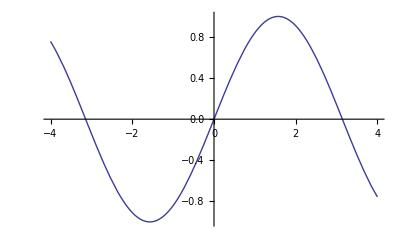

```mathematica
Plot[{Sin[α]},{α,-4,4}]
```

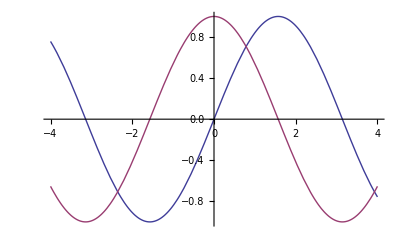

```mathematica
Plot[{Sin[α],Cos[α]},{α,-4,4}]
```

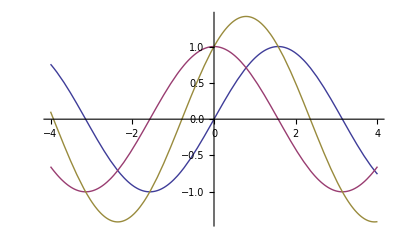

```mathematica
Plot[{Sin[α],Cos[α],Sin[α]+Cos[α]},{α,-4,4}]
```

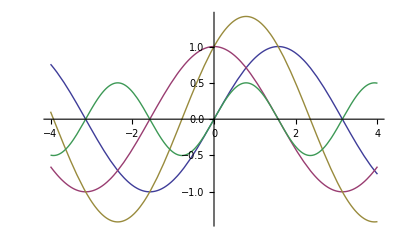

```mathematica
Plot[{Sin[α],Cos[α],Sin[α]+Cos[α],Sin[α]*Cos[α]},{α,-4,4}]
```

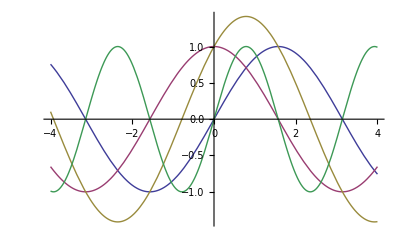

```mathematica
Plot[{Sin[α],Cos[α],Sin[α]+Cos[α],2*Sin[α]*Cos[α]},{α,-4,4}]
```

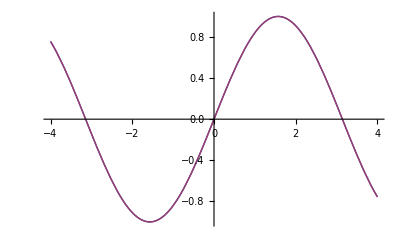

```mathematica
Plot[{Sin[α],2*Sin[α/2]*Cos[α/2]},{α,-4,4}]
```

```mathematica
Sin[α]==2*Sin[α/2]*Cos[α/2]
```

Sin[α]==2 Cos[α/2] Sin[α/2]

```mathematica
Plot[{Sin[α],-1+8(Sin[α/4+π/8]*Cos[α/4+π/8])^2},{α,-4,4}]
```

-Graphics-